# Double Trouble in Double Descent: Bias and Variance(s) in the Lazy Regime

This notebook provides the codes and the data used to obtain the various curves in the paper. 
These can be used by the interested reader to obtain new curves. 
The notations are P=# of features, N=# training samples, D=# input dimension, ψ1=P/D, ψ2=N/D
The details of all functions are found by typing ?NameOfFunction as usual in Mathematica

### Packages

Please ensure the files Computations.m and Plots.m are in the same folder as this notebook or change the path below.

```mathematica
Get[StringJoin[NotebookDirectory[],"Plots.m"]]
datadir=StringJoin[StringDelete[NotebookDirectory[],"/Mathematica"],"data/"];
```

## Figures

```mathematica
(*GENERATE DATA*)
(*{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=plotTermbyTermEvol["ψ1"->100,"ψ2"->0,"plot"->False, "NbPoints"->50, "minVal"-> -1, "maxVal"->4,"λ"->10^-5];*)
(*LOAD DATA*)
(*λ=10^-4*)
(*{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Uncompress["1:eJyV2gtYTHkfB/C/NuWVLtTKZtXoYlVsoTcRZuRa61Ishu3tbV3a4qWcymas3SOLUBJdSHrHpdsqmtBNmCSykqyodJtS7XTBxLK57ntm5nnOnHd+z///2J6enqfn2zlzZs7/fz7/75/Rq4OXBOghhEJ1mR8LgkLDAib+32863N8opPpSXKWQbKXHvnV5fK18pZVFz6w1T5hcnBQ13iJfO8+b4fJwz41uJhfwmp/sLtbOB/stKr1tL1cenynov31VO1+zPTDbOKaDyUPa5hzWK9POS1Iik5Yq2pjce//zo4U3tPNPVX8gU55/7qY3xre184b8jcpvJq/4JvCKcbV2HvPyhIR5C0wurzR9/uY37ZyvfHtvqpk8anBH7oKH2nlrhxlzBTeZXFrwQyx6pJ1HMQcLrYqZfNDc6VK9Zu18ykCnDFlHPJOjpxHhvFbtXPXqwnN8CvnFz5w287F2fsjWk/m+xuTRro7Hv+rQzpVnNyupZPKSuzOefPG7dt6pvPyk+0y+pa6m7YZcO1e//TomT9/tlGPTrZ3vZO4ONbiZya18RXdm9mjnyrv78kQrk48N2uFu36udm6huQDuTu8TpTHwM8gLV7etk8p2SZL+IJ9q5anhFdDG5vaGtgwLkqo/XrJdP0VPSao95P9XOVZcnecocH//kr+2pIHeIUN4hBZMvzvBOaAK5avi+7GPOv+bngocmz7Tze0LlBHrBpwS7DWXxU0Fup7x9h/5gji+OWnvaF+Sql5e95FPShH0Xvo8AeaW98i/+5FP+wlUTXWJBrpq+2/uZ8wcebS89AfJQ1QR9zad4NhMrHuaC/KZy+Fq8ZfK9lxM+lIBcdfrAd8z1Wd9xF98A+SbVBHzPpzK/HVqlWwVy5d2bMvAv5vOxpKnA+yBXPz+QgCq5QHWZ14JcPT6ZXLQX/b69HuTq8TFAQIU05q0e1ABy9fzUEVDLnDZKBzeCXP18Y/Kv6osuFsFc/Xz5RECl2M3zd2kCuXr86QooKjxhWAzM1fOTySuHfymrgrn6+TtQQB1r/LEINYNcPf/0BFRodzXvC5irxzeTWySZW86Bufr5oi+gWjz1b/vCXO3DIAGVaeKZHqzMP04ThLwH2JzBa4KQUaRHLl4ThBovh53Ha4KQXHd6AV4ThOIVkkt4TRC6kh4uxWuC0J6jNNBIowlCRRsG3sRrgtC8AiOgkUYTJL3bmnYXrwkSmzYFAY00miDB607vBwRNcs+ax9ThNUGKB/q8RrwmiM4o/NCC1wRVGAh02/CaoJNpr3Tb8ZogNFDWCbTSaIJ075omAa00mqAdCR6GXXhN0MHuRE+glUYTFNc2wgdopdEETQ0rdwAasZogtDn1fhPINZoIJn/ZGgI00mgiLZNmdIGc1QTxymQvFwBtWE2QeJZrOdSK1QQpeg1WtYGc1QTJR45cY4HXBM2/WPipJ14T1N9nNzsErwkq6fRaH4fXBM3K6EzPwWuCLgyt31+O1wR1hBworsNrQkvMpPc68Jrwsp+VvejBa+J/8NbmnF68JpmpUr/b3XhNzLKM/fhyvCZnN5VNbYDXx2riXeO6qe4xXhObVwkj3Nrwmvz0OPhUjwyvSb1o0rm2Frwmpg0++sYwZzWJ/NJ6/jqCJmVu02IboWasJhKzQ283Nv0NTY7Qa7NJmuRn20tImkh1pRdImlge/LSIpIlt2eIrBE3oV/MWXCNpMuSZIeguHE3oiDP0rwRNBO2F54AWHE3oqfUVQAuuJr8ffAO04GhisqFtUj1BE2d9B1OgBUcTZ8dTn4Fuw9EkcKtHLcg5muTWvrMDOUcT5wM+HuD1OZpcT7uUAa6fo8k26ykPQHfjaBKQ+/XYGrwm9NAAUe09vCZ0WEJIP7g/HE3GLNrAv4PXRFz0xfgosFrQaCIukjyuAeNDownKP/VsHDieo4lPaN2JSrwmn+/O2bsUXL9Gk4qV68KLwftnNaHrfnPLyASfn0YTg80K3SywGtF0k5w3w3UQuP+sJiGlPdOSfwCrDVYT2UTRPwpaOrGaNP7baYHTc6A9q0lazBZDoa8Cq4lzBZ0cn9qH1WTa7tFzSvvB8awmNbdunL96DNNdGU0Us6tCOhaD7s1qsnR1yeSwEND9WU1a7uS/vvgIfH6sJjWjYl3CdoLPn9XkQMeO22Gx97GaRKY0/5nhD8YHq4m7ffiS91638N0k973PVdF1rCYeMTdjA9LAapzVxCTOqMdqDFjNs5q4Xjr5vf2k/I/XRDot6xeSJrbL/jhH0sRvmBWxm+S9qQU7ZVxN9P3cid2kkXYmdRP6Q4wzqZvQNSlZQBuuJuFH0sHThNtNrqybQOwmeqX2pG4SEpxmQOom0ml3Z5G6Ca9hVE0DQZMoxXEJqZuEuBU0gZ00jiZHhjU3g9nE0WSJa3ApqZtYHhZSpG5StsapC8xmTjf5uthoDKmb2Nx6NZ7QTQSLE2X6hG5CW6SiS4RuQov6+hYSugk9wGn9DUI3kYaemWBP6CbeWyvcRIRuMmiOf34JoZsMiV849wXINZrYhrvr8gjdJN4r7sRsQjcxnzdxy2pCNyntXRItwncTgVxskhWD7yb0TUGZMAXfTUKGPbhqnIHvJoGmK4+vPYvvJqdH5EU6nMd3E8vCsFL3fHw3id14ijejEN9NPv8uUJRchO8m6x/wiw8U47uJ8wxHIf8Svpu4ddf6X4M5q8nXrxSn7eBOI6vJmFPZlhTMWU0+1BvV5sCc1eTCZ+XvGmHOapLcXLFX5/Lf6Ca5i1qJO10uPz0i7nRZUv7EbnJtwslCkibU9uuXSd1kqGt/KUkT102Z5SRNhCP1SN2ErsofSeomYoeIYFI3EZgnHyB1E/GAUAnQgqOJSW90ONCCo0l1kM03TQRNhM3PFSDnaDJOvtkY5BxNosO9+sC/+3A0OVt10RhcP0cTh5PyTrB25mgiXfy6Gqy9OZp4uQ5BVYRusu7XYBOwNtNoIj29+E4tWJtpNBE4bvvME4wfjSbolx37xSV4TcTryyvOgZ1ajibPZUlJYDXF0aTCku8C5o9GE3nAkvFVYDWn0aTyu62x49LxmszuurxbeBKvSarJ1RTfVLwmVyS7TvGOYjWhs7r15lfGYzWhsxv03CfHYTURZCYG/kBHYzVBkTrWsqQ9WE0yawMNkvfsxGpSzet2jHegsZq4TTFpt7suwmpS94JnbWC/BavJ1lvLn/mupLCa9Hve9b23ZhNWkxYzWmLrGITVBA2z3ZdUtxaviZ/5oaDZ32I1Sc5acSLymC9Wk/S31u1P81ZgNbEYIPRyPrkUq0ma+eQE69neH6/Jf96OCSdpMmRs1I8kTcK2vd9F0sRkzpFYkiYR4v8mkrpJ8rvRYpIm8R/awGzjaCJdGG0FZjO3m+xBP4PuxN3pMlxuBv4XAVeT8V08oBlHE/+WrHFgJ4SjiUDkvgxoxd3pGv7asZagiUzeugLsVHE0WduQWCojaJLiO9aJ1E2uTBq9itRN1hkdmkzqJqtn/auC1E18DrWbEroJjfgKG0I3obPrl+sQuok00uNZAaGbSIfMmL6A0E38fb23lJO6ibwlcyyhm5hsy+3ZSugmgSsK9pG6yfzlm8eTuolzwLuXVoRuIoxefpTUTTo/X7uZ1E1GBG7dS+gmqObxsgxCN/HfZZWzgtBNFKMODyJ1E+lQyShSN2n0NbQjdZPrOZ+ISN2kfGCOfDqhm2THVS8kdZPUIJ9EUje57oTcSd3E/Z8GnqRu8ltsaBypmwztO2NE6iavd7XfInWTPLfePlI30Vv6kFZ2k/8BJ5zPHA=="];*)
(*λ=10^-5*)
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Uncompress["1:eJyV2QtUTHsbx/F/g1K55Egqpwsl5FLIpaO3Nt5yJxHFUZHI5VS2kBcZqQiRIiH361GRSkQx0pEIXVxCmBSRSkIdJc6eZq09+8zT/1mvVsvS+mrMzJ7ms3+77vN8nRaoEkKWt+b+mLhouf+CQf/6SiT8iiXNHzXXuL+EDYjzSrJT6hanpK+10ytlvfGtoclF5e42+fqdPgHvZF0SuLtdhnIP/3LkvK3VG1m/Nv3hwEzlnh4btGdazSuui3dfU027qdwfbbrZkOfyUtaPDN07Kle5WzX/gyLZ7T92NF6dr9wjTcdxnwVcZ6qcdvo+VO4l3KOLDcrmuuR/9S9Unip36zayZyBF9v25A8s7v2y577JjiTQwdN7gVy3f/2tcJw9vud8ra/n5zeX64VaDh5qXt3z7D7he83RZqdk75f4s9Q/ZJ9cdPSd/T69Q7nbNT5CU64llBir175W7VvMBKuN6QPLNCW8qW35+ymWPL39I4/4q5Z5kK/sPKrjeNmm6lVm1ct/IHV1Wo5rrvb8fL9wBunmA7BHWcH34fI9aKejy41fL9Swzz3CjD8q9Mc/FSP/9J64Xv5d0dgTdc513fMfwL1wX+X0pWAF6bh/ZHajnesUUJ/so0OWvr7+5HmR6f9wZ0A/IXr5sgx0rrn6hMyEd9ObDp/2N63drzrjcBt2n+QA2cbffYf32vg9Bl79+ftixjqP1uz8qBp178KM91xGGDRh/5461FPTp3LPvNlmFYT2YzlkdS0DfLLt5IxHDXnqRHzcTdvnPJ9fNn2uLV8PefPPXWzHs5fYVEdtg7yk7fJGtGfZixf7AGNhdmx9AG4ad6Dlj1WHY5e8fqgxr2/lm25Owy959rNuoMWxReJrmGdjrZN/+iOtG58aRBNjlr7+2DLsg+c3Qc7DL39/UGdZQN6QsEXb561ODYbucndY/CfZs2dOrr8ndf+sc82TY5a9frutl2H5oocvfH9oxLFPfb3MK7PLXd3uGHbn94I8Weozsx8+tA8MWPzObcwF2+eu/I8Nm6G492UKX+6DFsKY9raXN/f/UhBBvkzhEE0JWic4jmhAyxP4CogkhDRsv0zUhhBmxUkLXhPt4OiML0YQYT2y4RdeE487P/x5dE0Is/ZcU0DUh5K2B/iO6JoQcnzAFaCTQhGh/agM0UmhCyFxnNaCRQhNCDhmGAI0UmhBx9+Dbb+iaEPHtOZff0jUhjH+3KUAjhSaEEc/aCTRSaEIkTPZ2oJFCE5K4ycAZaKTQhJA0uxrQFZqQW+JHi4A2Ck2IjXNYDugKTcgAL88uiCbEysLOCdGEGNUOC6ZrQsQhNqPP0TUhxLyHbxGiifEezdTWNVRNiP8T63W9QOc1YVZK/A16gM5r4jju+7aemqDzmtgs21K2nIDOa+I4VXpZtY6uCZnX5/2FD3RNnAdOS0l+T9ckoHSTC3lH12Tt4Ci1buV0Tazmmdimv6Zrkqm9yCatjK6Julf7T3WldE1a9wtc5Qk7r4lP94TA2ld0TR4ZPZ+1H3Zek3s+btkzYec1sTK83csEdl4TGzWRZgOiiW3MtsdPEE0svX+JlCCamFmVpsT/lCbV8+NRTTb/wDUZkZ+KaSJeU5GOaSLWmgS2i1ATJk4/G9NEekN0F9PEr0YVaCHURGtrE9guQk2KfJqeYJro9mSeY5rYZBa8wDTxMbQAXaiJ6qHEZ5gm5WvGFCGaSM6HPnyAaaL1vQRsO4EmxgfbTb6PaKL1Ln8p2I4CTbw/3zO/g2hS+Wb9PtAFmui4GVeC4yvQJEHny0hw/wWaTHG60QEcX4EmBrEu6uD5VWhyKdTjqC3QXqFJZeex2R2BxgpNXH//FqX7maqJR5fH1cfcVRiaJmPDnjYVPO+o3HlN/Nrk1p6y1FTuvCY7o0ZVWX3+RtVk/0K1IyYjPlI1cer0wbDbDnC2wmtStaAhNWkyOFviNen5VX/k/K3gbIzXRGV2sebs43lUTVITbsVu+gHOFnlN9lSctVkuukHVpH6SR2ud/uDaCa/Jn9oaEaKt4P2L1yRuXH8r9SDw/sdronvg17Nek8DZOK/JxperWPtZJ6iaVMf4TjXIOEzVJP5+eM6J8fuomtTXupKAhF1UTT6eyVyfNyaCqolkmbbDvdNhVE3WmyaJNGyCf0KT6D/PoJrUpSaimhi8TUE1aeyEbhOJ9kB0mxhXtkK3iYdrDLpNSKMI3SZjp/ZFt0lEciFFG7kmNatao9vEtO4SqsnVLGkJpomtqTu2TcglrxPYNiFNetHYNiE9wvpi24QssfPBtonHjpIl2DaxvGQ6CNsmm/NKcrFtYrw32R7bJuLpZsexbRKtrlMNukAT91XqvbFtYn92vTO2TU4e6r0a2Sbi6aXtdiPbROxjsxNeSVNsE0mVU2Ea/UoX0+3A4igJ/UrXA83+J/+TSb/S5XCJfZkLO6+JXa/ltlo36Nsk27vOaijsvCZbmmZ+ngQ7r8nn3msL5sDOa1KqEVTuDTuvya5Zw0r9YOc10V2anLUSdl6TX/ON+q2BndfEccO7oEDYeU3Stbp22gA7r8myMTPVN8LOa9IoGhARDDuvyWy7xZIQ2HlN0izVzobCzmuyJrar9ybYeU0WHNRpaKHLfeA06aL3YOnmGz+zTdJL8Ctdm+PxbWLtjW4TstcL3yaNf1/HNBHbJoLfqwg1IeprwbmxUJOI4+cp595yTYo27ES3Scw2f3SbMEciizFNfj9XB7aLUJPanK6gCzVxuDYJaCXUxFk3GJz7CTW5vS4aaCncJn1IW4q2ck2GhNSDbSjQJFGrvQo4NxRoIgn31biKaOLX4Y8L4PdyAk2KToQng9/rCTQpdl0kTkA0sX0gcjiFaDL37dI5RxFNtB/nNMXSNZF0H3WsNJquCWPxZWrnSLomw81K1oZvo2tyJ3NPh/BQqibSbN3UkLsbqJp4Oy1OvKW/lqqJdIPvoRWWK6maDFJN39U+dBlVk4C/QxPNzy2haqKqcsXI7qUXVRMrPfUprmPnUjX59uD71CzH2VRN3BtdQvZFO1M16eEW9rGP1lSqJppfd15Y+3U8VZPRXSoXRTnZUzVJqt2Y1PSUoWoS1mg3rN/J36ia7Hs5Qs+i0xCqJmeuHNDYc8qSqsnSsENq9s7mVE0K/6p18883pWpSuOV+nusKY6omkjT7Ga1U9X9CE4deK1BNjlwWo5oUum1BNbmcCJaYUBMS0wMsvX9povPlNKaJ9Kt2MqaJuPwi0EyoiYuGyV+YJr1jB4B3W6Em8aNSwJUkoSbTnTuAKylCTXa9zpJimhytzSrFNGFXz0R/b7Lmv37YNpE0rdPDton46DkvbJswV+4vxLYJ4zDYEtsmlhmf7mDbxKXdSHSbxJ6uPoZtk+07GqqwbfJJ+1svbJtYD1qNbRNmom9PbJsw0RM0sW3ibe4XgW2TctGbAmSbkLkLTbFtUux+dBm2TVLaXkzFtsmmsu2G2DYR55Z1w7aJts1eKbZNJv1WkYltk6tHhj/DtkkOCX6CbZNYfY0MbJuc8v7FDNsmKxy6B2LbZMfRKe2xbRKcPEsV2yYWKfnh2DY5tHvbVWybtDoQHo9tkzEmVQuwbeIZZ/4V2yYjIvWat8k//X1qOg=="];
```

```mathematica
title=StringJoin[datadir,"error_lowreg.json"];
Export[title,{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}];
```

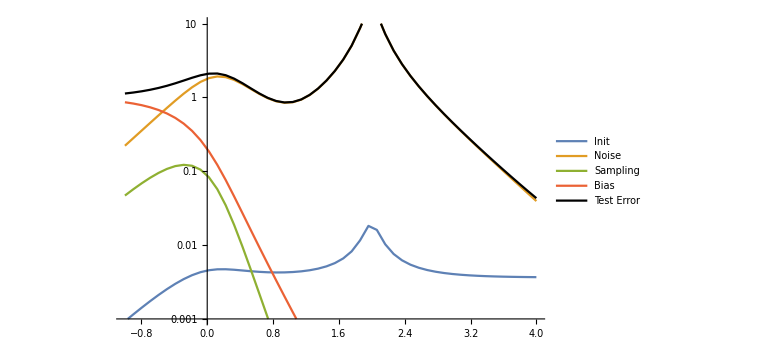
-Graphics-Log_10(N/D)

```mathematica
{varIn,varNoise,varData,bias,tot,plotlowreg}=plotBiasVarRatioEvol["legPos"->{.825,.8},"plotRange"->{0.001,10},"ψ1"->.0,"ψ2"->0.0,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"λ"->10^-1,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 2.,"k"->1,"logy"->True,"pts"->{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}];
plotlowreg
```

```mathematica
(*GENERATE DATA*)
(*{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}=plotTermbyTermEvol["ψ1"->100,"ψ2"->0,"plot"->False, "NbPoints"->50, "minVal"-> -1, "maxVal"->4, "λ"->10^-3];*)
(*LOAD DATA*)
(*λ=10^-1*)
(*{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}=Uncompress["1:eJyN2Qc01f8fx3HK+vkl4pIkyUz5adCQ6nsrRQkhmX8jUknrK0pGlzJ/yKgklVGRyM7moqKMhpWVrln9Ul0ZWeVvnPP5/f/3c96dOk7nOC/jut/x8HSXHTypb8fFxsbmyDH1396jjmfs1v7fe3P+9z2SbeYfk04uFxrXXN+aTrDsJkvFPu2w+UwnR06fXpCn94h1z9iq0uhb/g+dZNpd9u21zWPdeS10SqsUPtDJtC8OrlsUill3G/cjyfxBPXTStjsnfE1zKeteeNMrwoDZSSfbVEYDvXmesu7CMx/AoJN7KRODPxOese6t2cen3+jk5m/uw0tzq1n3oKHY9KkfgU4Od7uNr4x8xboT0z/e2Cs6yckY+uI5t4517+ihTD2CiqnnJ1rZcF1wA+vuN/XJxkvz6STvEhO1Rvkm1l2Vc1UCo+cKnQyVEE5aWtjCus98d+NUghwe/rCsfP1b1j1MZvfUWxlBMibZF9B83rHu01+dUlhNkPJae5qiXjJY997phx9RR5BdX98NWxV1sO6zP34TQWamG30QC+xk3S9OHR2St50g4yPa7ahbulj36aM7FNtBkLauLq4n6rBdYOYAdBPkYIhZVrleN+ueM3P4eglyldtbbloBts+cXuc+EmRw+Q61e0I9rPvM00vpm3p+Jr47DJpj+8zDS/9CkHMrlHPqIrF9xbnpI8QkSD+FD8161dg+c/oO9ROkm3LdkOIwtr82nr6ABgjypmjQ01bRXtZddvrwhQ0SZFo/r0nEOmyf+faMIYKM3Sqmb6uN7dUK0x/xnSAL5RxXL7bG9pnL132EIJPKPQJOnsZ2x5kLdJQgrU72bRj2wPaK6dNXbJwgRT/5eK8IwPaZL39kgiD3r7YNIcOx/cTMBfiDIP/zXvW9VBS2Tx89Vc5JgnQ9Twv2jMX22fsHG5U8mf+C9iwe22fPz6m9yNS4VD4J22fPD3Yq6VsjI1SRgu2z1+ccKhkUEmFbkY7ts/e3qV10wd6JHVnYPnt/mUslpa8LkQbZ2D57/nFQSREeXneeXGyfvT6ndgGxlbfJPGyfvf9yUknFh/4Pb+dj++z1x0UlC/o36UYUYPvs+T21H3KW23+oENtn7y/cVLLUcC2vQBG2z/rAQyUzNBI9bk3vv6UJbSVRwBaZCGpSYvEf02e6KaAmjFdSpc8YmEZIE7YHjZN7fmaBmljZR1tyeeeCmpSUiHn3ORWCmsQU2wgn2JWAmqj82SKqUVoGasKcQ17xUce0QprUN7Rx7/5YAWpSVhF0bGdiJahJ/ISHwyJaDaiJb+ZxpX3rMM2QJqJJC+iKGa9BTUKTT/JtXotphzSZMDAudU+pBzVp+GOcz0yiEdTE/lp4/1mXN6AmX8sv5O/Kw7REmghMjJVUNDeDmqS4fM5yb8Y0RZrkL7qi1pfbCmpytqhFa9ClDdSk4UGzNnUppjHSZOHGc6p1SdiONFF2M6ookGoHNVn7nWNNjw+2I03M7+rb/2jBdqRJx+La4qPLsN8GkCYVRrpO6ubYjjTp9HXMswzCdqQJRX6DnlY2tiNN5sZqBZk1YTvSRMBZ3SttENuRJnRRbpoEF/bbCtKE4nf5Qi8/tiNN9AYz0jlFsR1pUr3ris9jCWxHmoTJv71tJoPtSJOg5aEpk8uxHWlyVtNdtFkR25EmUeGv9/CuxnakiVrtqp7UtdiONFHKaEvtUMF2pMl8csw+cz22I03yHTpd123EdqTJleZedydVbP9Xk0yeAo9N2I40aRG8GGKqhu1IkwP3ncsENjN+UxO2JvVE8QcPQE2o+R6yKypTQU3Yjo7w+XdlgJowihU3bjLNBjWJ2Xoy+LBOPqzJizax9kKsbZAmzx47aWtXYm2DNGFOlFOljJ+AmtwX7Gn/+b4c1OTItrK7h7Weg5qYCxqs09GsAjWh7areahWHtRHSJI5JOdylgGmDNMm2OOKcWIl9PtLEOUokVzYc+/5IEyOJrsmdqdjjR5rYFp0/pmGKaYk00TUYDTV9iT1/SBPfuE9iBIFpjTSxvrfAOuk6HdREUbl5tFikANQkbktO0+t5OaAma98NrJCnZYKa7FbXqi51SIPb5Ir1cvbwJFCTrWxRLmXCCaAmyw3Dn5zZfQfU5OXz7FcuIjGgJtsS437019wANZFJ2dOVoXMN1KQq1N/jSWAYqMkHPvVz0fXBoCbPfTRH3aL8QU1WnFc5fXW7N6hJ3BmPKv57nqAmt7qL+Es13EFNEvj0Jfp2nwM1OXDxnsSwzBlQk/cyupWWWadATQIkDkkezTwGahIpJDkk+90O1ES5mrMo8w8bUJPSf4zc3ly2BDWJFw1sXKlgCmrCruG/qCnFENTkPFfSk79H9EBN/tIJ6Yx+rg1q4pOymp+eqglq0rn2kra1kzqoicJcpas6g9Tf1WQ02F9D7hdtEmG1Y/nzh7AmZx593R72izaxk1xpcgduE0kXnoxIcbhNTn388mrbJHa3QZrc7+3KmCcDt8mlKpdn4WfhNnmyy81xzyB2t0SabPbN9nMPh9sk+S/7rVt14TbZ1zWyxUIabpNxqRYbMy64TbzSUgQ1L8JtclV+3LAT/0sc0mS95534URrcJuruSuM1/dhf6pAmHqPC9T3acJsEWNsExQbDbRLmXHlqJBVuEzMd59GjaXCbdJ0v/+kSArfJwjjtw3/qw20iF+uys+o7tiNNltm6HqJfgtvEYiGbyug4tiNN3mr3m9tZwW0ibBE3mp0Ft0njgltK+uPYjjTRFmutN1gPt0nFqr3HLh+G2+TrnRv1V0PgNmnyoukWZsBtwqxfmCP9Em6T17eu0ei92I40qazt/st8DNuRJl+EQwP0OeE2iRDKyKfMg9tEKvjAybQFcJvU+Mu6G4nAbZLM9tNaWQxuk0fhXnF2S+A2Ub3ez+SThNsk4PYPmW1ScJs8WBL+JwVvK6SJwsF7lAhZuE0+8O3rfiMHt8nfDm1VHfJwm3x5GKxUjLcb0iRv0rfhjMJvt4nTgz6BVXCbsFGMPKo3wG0Sk/BublUg3CYlqdwuHQPY6y5IE0ZaLtWkEXvdBWnC6BVXF1kDt8krU625WS5wm5QcSKrUmXgMaiLacfjgEA1uEyZ7YW5fM/a6DNIky97TkP8FrEmIuWDO0DK4TWT6BnluxGM70oRG3Rwpqgm3iajZmGM6BW6T/NNzVHM3wG3yWb0998Yn7OdHmvi91ZfLsYfbRExx1TbRHuz5R5rcp2w6u3wUO35IE3FqY83Cv7E2RZoUblszfisca1ukicUAF2fhQrhN4qMZTFMhuE1aE+1O5Ixh5z/SZDj5D67YK/GgJvoDd1ss2uJATRoSiqw3OUWDmjyX2j5yRxlukwyfQUHbmqugJmXF7wRvSsJtwn16d+bIUrhNiqXfeL7mgNvE+cPda/OfXgI1UU8Xqw/fDLfJoNeFu98i3UBNzo3U9jvmnQU1+cEfksJMdgQ12W8iLvJoH9wmOlzNSv18cJt0zwtTaTgOtwnzhppaRcRBUJNRTs/aploLUJNM23mWJwJNQE2SKjis3inCbcKfbJf3LBBuE/mOBNo3EbhNCC2BhpjFcJtYiPea3RjbAWriRSpdCAj+3TahXm7NC/6MHS2kCY33+wb5I9jZgDQp4Rc365XDzrZ/2yThxHG/44GgJjRCI4nvYzjcJoyhxTbxUaAmTe4+tqcmsasZaUL9Md/SrBxrL6RJ1qGb+wQ3Ym2FNHEosDI3vI7dzZAmbrfZB9R4i0BNxoJfMb+pYW2ENOlkqNlzHsDu5kiTu04D7XeTMK2QJmFNXo4181+CmqQJTvoUJWJtgzS5/zE1dFUS1jZIk5LgemtuGtYuSJPh7banbKSwdkGaxMxXMRUIxdoFaaJRap8r+AJrF6SJD99BY8O3WLsgTazZE1sSH2PtgjRZIuaTsMQHbpMayY/JYQpwm/BVNHH4ZcBtYtamm8wuC7eJo63lT69LcJs8vSP9SKgebpNyhzrVPSJwm9Tqiyw11obbxOSs/XcRV7hNAoZ9gymxcJtssJTmu10Ct4kvx6Hm5y1wm/RYH1tNY8JtEiOesHMbO9wmOz9vHs7lgdukl/pZ7J/5cJuMUBftn0eB26QyeqBeG3/dBmnibak7Ur8YbpNTCr1hpfjrOkiTjz+D+JSWwW2yLsZ032ppuE2GLur5tODtgjSp9FxRovaLNqn0CnO1+kWbZGZ4Cxn8ok04F15fIj7VJv8FRZxb6Q=="];*)
(*λ=10^-2*)
(*{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}=Uncompress["1:eJyN2QlUjPsfx/HHaCMpRN0umUupcCsJWZ+5oroiSlGo/OO2yPqE66YyKVt0W9CiMtMmiRRJZZmiha4lhCIpKmlTaBFX/6nO+fX/z/d8n8PpOKfzoaae5TXvmV+ctlk5y1AU5SEl/mupm8dOZ4P/+4zzv58xVN+fVhGTe8HHavvqS7TEbjderdF4Q7OI4T1wWhojnSm5X1pg+OxQYYP4/7+Y3tbmmiO5D3WwyPtHp17E8IdkqxgLRZL7Bm/X84qBtSJGeGfi0ht1tyT369H7w1e2vhExXPfoZNOAQsl9dN8/qBJ//SsxMtn3iiX3l5lbej/Ejy9tiIfezYeSe2B7bLr4RxAxJTWJ+l0ZjyV3uvfH6y4RMUpSKRe+1D+V3KtrlcWPoEjEBN8dq7tvZ7nkflj8n23H54iYtMjYnKkmryT32dJ6SVW1J0RM2Qdu0ldBleTe991tL9JMlj2/yC76jeQeqvG7+OMWzZR5X/Pd5Fsjufd+deXr92jG2qJkouvcOsm9rvfhhz+hGX/TbxlNN95J7v0/fhnN8CojzDSl30vufuKjwwytFH//6H3bOkY1SO69R7c9tppmVoywGPa1FexKfQeghmYuHdDZOSihUXK/2nf46mim3v7+1UDDJsm97/Ta855mdDWddxgkg73v16vcRDNeuoIKF9lmyb3v4aW30MwUvxfVMSvBPnlP7xFqpRkD+ewHTiFg7zt929toZsyoRWeO3Qb7I9veC+gTzdxxKu+0bwK7Zu/hC/1MM84r79onKLRI7n3fvqqdZi4f/V5Tog32ezq9/6KTZmzDEi3kabD3Xb7eXeLH5+E97TdLsHv0XaBfaOZPjZzKaevBXtR7+qp9pRmr2YZ5f24Ge9+Xd/1GM7d1HuYH7Qb71r4L8F+a2Ziwe/prH7D3Hr3Z0j0041Bvsi7rANj77x8Uj3m5O8PE4SjY+89P8f6lwyhRNhjs/efHIB4zubJbr/o42PuvTw6PiT5JH1IMB3v//U28Sx1NyUyLBHv//WUwj9G/+2Xzqyiw959/Ujzma5egMzkG7P3Xp3jf6HhouJYA7P33X2ke0/Fu619OQrD3X38yPOa25cEwl1iw95/f4j3jNH2HjgN7//1Flse8alN9+BHu/T7I8ZgxayePOhQv3n9IE4rSHrG8+xyqCRUcrz1cMw3VhNo+JF53yWVUE8roSMnZHqAR0YQqqde/YXcN1YT6VqftNzMX1YSi9sekTrqNakL5715tfBBoRDShXvw07OA6oBHRhMopeNyT+gDVhP/ryR71vEeoJtSwhlthW0pRTfirZ3GcHZ+jmuSqWZ8vO/kC1YS/bJJfq3Qlqom+M5X8azHQimgi1Gouoo8BrYgm+lcP5mw2BFoRTYS63eYhl2tRTeQedxU4cIBWRJOzIXKz1Lj1qCYayo0KXCWgGdHEVVHLJ/M52IkmQpmJg+K9gGZEk+JP7lauUkAzoskY3hT/Ng+wE03m0PU7/noIdqJJVWBgVpAa0I5ostAgfPRkW7ATTbqW9PCzA8BONDnf5fVlQQbYiSalL1ttHZ6BnWjikL3q3NaPYCeaxHlnfj80BGhINHk3o6H977FgJ5ootQuNF0wFO9Fk8lU9L93ZYCeaZIb8ub3CGOxEkwmaSbapS8FONLH3HSzdBZ8tEE0sPq00/m4HdqJJ/l8CwRcHsBNNFpo3CVQ3gJ1oUuyafcLXGexEk5UbW0dau4GdaNIztlvrnDvYiSbrG61tIrcgz5bE+y7OHw7Tt4GdaJLhqdZ2cDvYiSaNo+z0hTuaf1QToVVcyszzuCa8M0GXZNNxTapCFH0CM3BNlK6t1C/OwjW5M4Jpr7yBa7LzwVtBZx6uSfD0mdF/F+CadKsqa+XdxTXJ7+YkBAMtBjQpHO9z/RPQgmhCHZN9b5QPtCCa8IMvhJf6AC2IJlRr5Y2gYtA2A5o8vvghmvcS18SivP0/oWAnmnCFq1zc04FGRJMqx+XPvJ+XoZpQwq2yTc7PUE0Of36/SzX3CaqJWHO9k9rg90c0WTGlyFQu6D6qCS/3PueMHTh+RJONPqdNdmWA4080yR36It39BGhfoske68KI1EegnYkmu+3HTQjhgWc7RBONN7saa2yuopromzwNVuoEz7aIJnUTgqKChoPri2gy+5JboueYC6gmVYcdw27cPItqskPlkDfTk4BqUl175MjFglhUk7vLPjdwOadRTUY9K7jPNYlENbljma1uPf8kqklZVUmwWUkIqomqUYvKyyeBqCb7q5nkmpbDqCYzli9aYVXij2pyetSkzIdrfFFN0q+qyAa990I12WCbmKSptAfVJNLF3sV08E68TWyfdK+L245q4u83IcIm3h3VpLNT64nTJ2dUk71mxZ2GChtQTe7nhxQ9PO2IajJ5ek3yu7lrflQT3jzjxb4sbULJm3vmXMQ1oRTCF7WDV8oGNGn17L4cxdImZssuZ9aAV8oGNEkrk26uAVf7gCbDnI/rlYG7xYAm67KlTk9laZOW6CFOneBuNaBJQvKaYwtY2oSaaH/Bj6VN/Oo8RVNY2sToTaaVGkubaMvPfmuBtwmvUmGty03wShrRhD8psjThDN4m+vkFzWZueJuUXOEcmDYSb5MVXk9H/xyKt0mauXpHfDV4pY1o8vmwm6schbdJ8D2efVwr2Ikm/KjFb7Ky8DZZ6CSbN8oBb5O65pGuRnVgJ5p4DN2yQ3kV3iY5G1XLatLxNrH3nfZmzr9gJ5qEGckfU5iLt4l2qF/2gy14mxRIJ//MD8fbxMfnu1phNt4msptWze96ircJP1QgpdcMdqJJgGaU13IKbxPVc0yeshLeJnunGNxTGYe3yfr8g/efauFtovjH3NVX9PE2KY/oOTrUCG+TGWZG/moL8DYxWBwwXB22EdHk5LqbjcameJvQckLBpSV4m/yz3qfxyDK8TUI76jg1y/E2odY2HHpmibdJeXqEnQdsM6JJZ/OS+Xet8TYxKhS61dj8cJtwzU2tMlJwTbiVv0zKZnmlq3XR55e6LG2Slj5uri1Lm0R0qDyyYWmTiA8+UxNZ2iQjVTdsCkubcB0nuS9haRNnzsYIDkub7LtydoiApU3OmaxLcsTbhAoTpoyTw9uEr6kV7knjbcI/MqNEQ8DySpfI5daTMrATTYQZvzfsqgRfn2iy/jn14LcG8PiIJsJHJ86oO4L3jYgm3BBB8dzT4H0nosn6vfpB2yrA+1ZEE67IsKK2BbzSSDThvhr+aVUYeDZANPEv5TTEw2cTRBNu4ZsVZnbg2QjRRDXibc9qafBshmiS1TZh+PHQK6gmmUrL95q+Bm1BNFEX7c9XOAXagmiyelz8v4L9oC2IJh4pg+QUzUFbEE1CpJPPLb4vRDVJmfBN59XjKFSTsWcrXqsNDUc1qXsdv8VS+TiqienIgHKDU0GoJrdot+GJUwNQTbZOF3pOSD2AalKbFVrLtIN2IJqofdmz7HuuN6pJc1wRX+cMaAeiycwxm8xz3UE7EE3uFN5q0G4E7UA0aTKQcX4rtxnVJFCqZZj1HBdUk8Kn3RavFoB2IJocUZoX71sD2oFo4sWZYdq5eQ2qieGj0W7OtTaoJh+tLj6O17BCNVGfGSUzdYTFj2qSaxB6SmYXronQLYBZ7oNrsiJ7ZfU/yNnQq0nw9piE38DZNqAJ1363jnUYrklrhVZrrgDXZDvHuXjHGVwTfcHCOi/QVgOa5BQs/fU1uFsMaOJVIHpI3cTbpEC5NJXORzXhf5jeUVwE7pZEk1yhZedME6AV0YR6HVCelwju5gOaJB4YFmuKa0Ldndw+pwa8r0I0UfL6eZ97TDWqSfBX3mj54LeoJl2R89978fA2UepyTU9NxdtE414TR74KvK9CNDnvmLbCogJvkwbxgwtLwdtEWSOuY4sN3ibnYzcluVbhbSKotxSoWOFtsufjh/c/XcTbJDLbZt68r3ibWH9Mp07Nxtsk0a35+rXNeJtkaVCu6WF4m8w5sSZIm6VNNvw08YIPS5t4zlhjWNKEt8nLR0+fS7G0iUawmX+5It4mllrndtXD912IJrEOqbkXWdrEKT7qVBhLm2yqUIxpm4W3SZzOFCMZljbxWaLhpcDSJpdmrV87k6VNwo8K9yWxtMmJ14FFfJY2CbGM8a5gaZOk0lqbEpY2GfMhb/5WljZJGPxRuoClTeRL57VUidvkv2MYSuo="];*)
(*λ=10^-3*)
{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}=Uncompress["1:eJyN2Qs0lOkDx/FXUVjlstWK3YwyuSxSzVa6mLeLlNS6FIPISFIxeGUplyZKlJSSSy4NpWy0uZXLEspGKcqicmsKyQiDakup/wznvOM/T89z6jid4/zMmMs785nvS93Z09J1CoZhPpKC/8z2+Ox3XfR/302a+B2Bjf3jlxGYAT5vtUsuXWxfcIXbNaPkjWAvpOLNlALx3XFLRY22f49gN7uhNSRdKr6ffJeaY0R7Jdh5W67z9G+L7yVJIXFW/JeCnVk3YJd/V3xvOnZ35BHjuWA3l5g5b8UD8Z029gNPBXuLm8Rin8fi+xmNjYKv+jKCzTAuo7s2iu8vBPcuKaRKsJvIsYKHn4nvhlLCRyBfsM+sMHL/0v7tPYZO4NO0qHM0Xn779pfRCSz257yZxZ3ffnwf0Ilyid1Hlil2f/v6GwSXt3SZZyDbI7633PQQftEJp7v6jFvJPPGdPvYAcQWXP2zGmdfUK74rjD1BnYI9Sk95b+Wbbz8+3XTCQJKa43qgT3zPNRL+Ap7g8kqJYXKT+8X3UMGzS8j204nsJxqcn9yBXcdfeA/5dCI+MCH9RAmwjz9/Q3TCPLjLyHoE2D89Yqip9A7TiYx3l7e2aA+I7zuD3LLkT76jE9KPZZqctgD7A23hDfiPTmjMXbvNcS+wjx9fH+hEiebXhQWHgD1ZePgSI3SCnxsW1nkK2Meevhmf6UTk7PdSSknAzhp7AkfpRGKtvL5BOrCPHz9f6UTSfcmeL5nALrjza3cGYTgRb1tJzMgB9q2CR99xiwRO0M2OBHTkA3u48OrVJuEEZdAsrqIA2Mdfn4Ldf82L1L4iYB+7+orJOPGc+4f7ub+BnSp8+s5I4kRzs++25hJgtx27A1I4cUnz+J2GUmAff/+YghN3PkX8FXsL2IXvPoZSU3FiR7YMS68M2N8LL94k2F1e22AXwX38+JPGibnyGYNfwH38/U0GJw5YumEm5cA+fnzK4oS15c9nD4F7lfDhVfkBJ/YurZyWBe7jx69g31jtoVAH7uPvD3I4kf5jRDoP3MeP72k4cbH6lAtWAezxwpef43ScMFLWi1QE9/HjXx4nVs/WmKUG7uM+KAhuf0DUXW3h/n2aYBR1U7VMuCbYBtdlX7PhmmD8G4r4DbgmmJfq04BiuCaY6eSnnuVwTTAVrQ6zSrgmGPNlL68aqgnGXtyp4FAL1QTDFo5I2tVDNcHY8ayrWBNUE4zzyuKdTjNcE0z+OutfQCNSEyz7UNqfXS/gmmh9jHhiB2hEaoJ97v41J/4VXBMGRS415DVcE6Pzxv8pARqRmmCJcw90WgAaiTTJONqRZgZoRGqCOTt7RSkAGpGalBuyipf/CeykJvjW/j4ZClwTbvT6AbtAYCc1OS0T2/nyDrCTmngZKo9KfwJ2UhP8iNWmZVS4JhymHk/DGK4JpV01W8IBrom+M5acxoJrYucS5BkZANekeN0z+49H4JpUEvaz2k7ANcnk/r6y7zRcE4Xi2gXXYuCa0ErqmQfj4Jro1LA7YhPgmigGJYUtTIRr8papVrQP1JjU5FyCeoJDMlwTvxDzcuUUuCbTFfN0r4I7qcm+whmnVS/ANdnzyHbZfnAnNalTcMgtAndSk7Amzio+uJOaSCgnqaly4Jo4VgdzV4I7qYnDQkV/G3AnNVkbRfN0B3dSkyJp6sdAzvdrwlezcMpCaFJod/tTDkKTGHvJmpsITfiZetwShCbY9IPrgHaZoEn1wCa5KoQmX7qu8YB2maBJT+mrIaBdJmjiw3zbCrSLSJPyUv6n+5B2EWrCfRsQ/KEVrgnHoyHDH6GJV1jpq5o2uCZ8VnHj5ha4JspL3Oa+fgLXpF3ZM3F/A1yTaUahCWDbiTTJTV+iaQBoTGrC3mz3WP7f+1BN2OvojZmFgPakJtgSzb5nxcDzK9JkqbzV4kxgJzUxiG57E2UOXL+oTXYUhmgy70E1kau915F2CLj9pCaRsWt2J62pgWpyJjJdz3kTsJOa9GSG/9rmAlw/qclFRoXrzVjg9pOaqN+OmCPxC9DupCYMbBa1zvQOVBO/tujYS+7ApzVSk1+spVZle/8N1URf/kR8eCLw+iY1qa4sDNRlAec2SE2M7i/foFp/DarJP38nR9mOXoFqcun6ufO8pRehmnB1t8hsz02BarLyfMKz9b7xUE0mDT1/P+JzFqrJlO3mc+d2R0E1SU6dQdl0NByqCdvLI63PKxSqiZVnmtTUumCoJixq1KQdrv5QTUwzDT9oWfhANSmwXK9VepYF1eT4c2fflwvdoJq47p/0RU9j53drUl4bm34VoYmbSnUeqk023JHvyEdoElM6KoNqk7OyD3RQbaImqz4CvFomaLJ718oIRJtgzVe+9D6Ea4LvLNdWQbQJt3MwtRiijVATisIZDhfQRqQJZWqe7DGEJqeZo6wyVJsEzTH8DdEmCvbdQz6INnlUFn7bEdEm2SMmDQPAmTSRJvKHM00XINrEKFzRQQfRJlXVsXv6gZ3UhL3jZYj0MXibOP20/GnaKLCTmmCe7d6ptvA24fpcG67iwNuE01qvG/0E3iaX0qyVDknA28Qsuz3ATh3eJnK+tJNMQ3ib1NBWXNi1Cd4mOudflLYy4G1yfm8Rrc8Z3iY/R1H8/MEzeaQm6ndrNDW94G1yTzPGznc/vE1MZqYllfrB2+Ty29X81QfhbcLY1522KBDeJkZr2kzzguBtctMo26Y9GN4mGi/ex1WBZypJTajvTScFs+FtUpC1c0TuMLxN/rBzXB4E7qQmoSbPAxrBndSEuU/qrUoIvE0W6ay4bgHupCYFx7obA8Gd1GRqw0ZuCriTmgy3DJQWgTupyYJpQ8O1Id/fJlylxW2oM12Uxw0ZqDbJ1p3jjGyTlkB7VJvwWVH8CoQm9QPz04DPZhM0aVvu7YJqE8f5simINsF5YfneiDbB22kRa1FtYq6etBnRJpQUP7tUoD0maDLZQqoUuLxIE4bZwPGPwO8XaeK09aD1KuBMnEgT2mJZF0dAS5Em7v0niByItkJNvPU9LG8AbSDSxJDxeVst0JaiNrFK3EErAf6uJjrTlZxicMIf+LucSJPpa3ryQ4HPviJNHC7/5kcDPvuSmnjhw4t0ZYDPvqQm+LVRygbdNKgmG+KD1VuvJUE1cWMucLFLi4Vq0l9subG/LRqqiXRCQGbAkkioJtLzqqhMkzCoJpIPQ+NOxR+GamKx3Wo45kEAVBO/9bsYbu99oZrwmg2U2XbeUE2u/OeoruOxD6qJjkXWUF3WLqgmxW2vV5xQZ0I1Ucr/+kvhDHuoJre8om8N7N4G1eTxufxVlb3mUE26s7YanCw3hWqyZMes/EGqMVQTql6F3mABDtWEzh1eK+e5HKrJ0rILKve6aFBNGgM5OS5HDaCa8Fqfy9uo6UA12WnroPj6sgZUE+1TK0IrrShQTWLODPaPPJr93Zo43ZqiARxNEzRh/2FfwEZoIr3XkHEcoYl18uyrMQhN7ke8U+UgNFn3F687A6FJ4yMZ6TxUm9x5mwJoNuFM13Tr3B/+gWtSHvhwUBI40yPSBDtofy4aOJMk0gTf43/1GfB3FZEm/pUh9zlcRJtk+vbHdcA18TrQ7TgP0SbVWqrvliDa5JIN3bMV0SZmH3KbqIg26Sq/W0CFtwk7qG7f7DfwNsG/Fle0HoW3CXbYQ0Ua0SZOBb15vyPahB3cG5eIaJNsyVU2/og2CRz5MdML0SbVm/0eWiDa5NJPFqrbEW1SpOes5Ixok0jj2zbNiDapVrkQ3otoE+spdev8EG2iVMYzmY9oE5cmrfz9iDY5W7JWDdUmKvr1p1Ftso2SYYtqk+1hG5VQbWLztPJXVJtoFpT4otqkLyyiOwjRJv4n3btQbVL88LU2qk0+e/ezUG0y9WZjD6pNjBNpV1BtYpt0tg7VJsbtm1pQbWKx9GsRqk08rjfyhW3yP95I4ws="];
```

```mathematica
title=StringJoin[datadir,"error_highreg.json"];
Export[title,{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}];
```

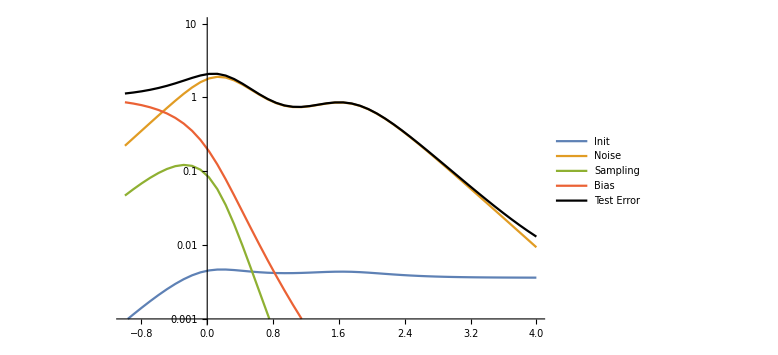
-Graphics-Log_10(N/D)

```mathematica
{varIn,varNoise,varData,bias,tot,plothighreg}=plotBiasVarRatioEvol["legPos"->{.825,.8},"plotRange"->{0.001,10},"ψ1"->1,"ψ2"->0.0,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"λ"->10^-1,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 2.0,"k"->1,"logy"->True, "legPos"->{.1,.3},"pts"->{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}];
plothighreg
```